```mathematica
Time[Expr_]:=AbsoluteTiming[Expr][[1]];
```

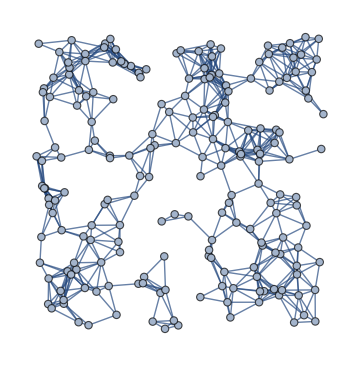
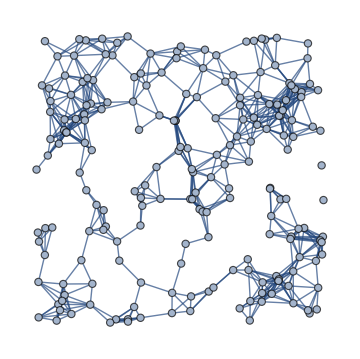

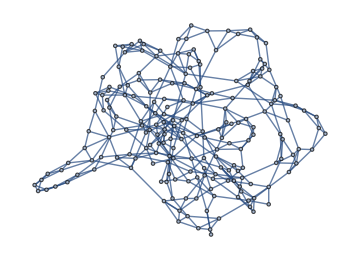
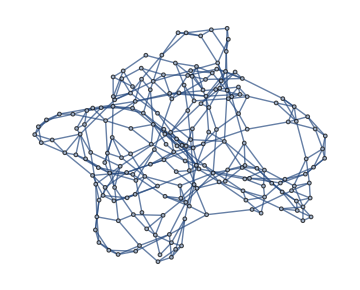

```mathematica
H1=RandomGraph[SpatialGraphDistribution[200,0.115],2,EdgeWeight->{_:> RandomInteger[{1,5}]},ImageSize->Medium]
H2=RandomGraph[WattsStrogatzGraphDistribution[200,0.135,2],2,EdgeWeight->{_:> RandomInteger[{1,5}]},ImageSize->Medium]
```

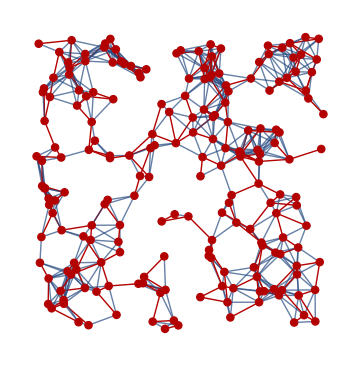
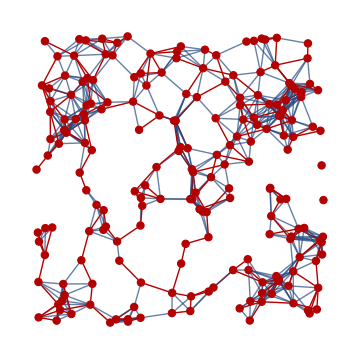
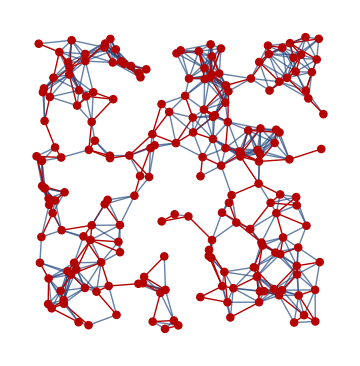
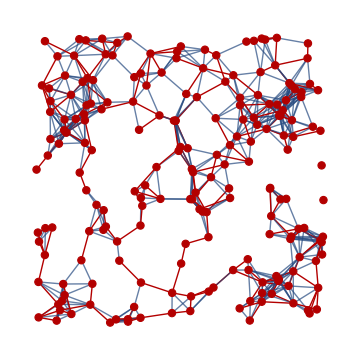

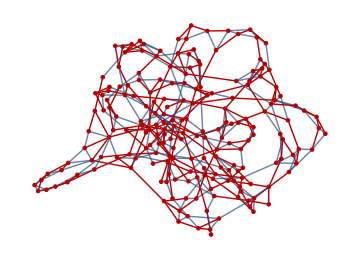
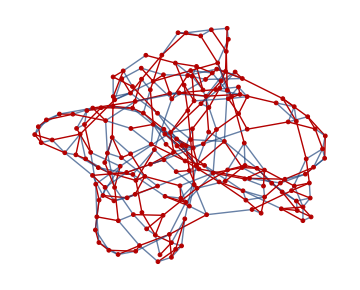
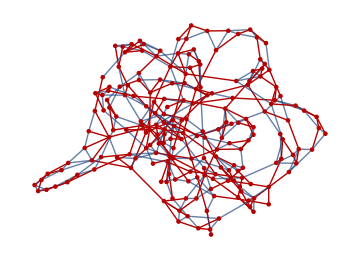
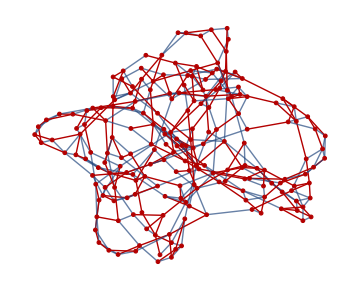

```mathematica
{HighlightGraph[#,FindSpanningTree[#,Method-> "Kruskal"],ImageSize->Medium]&/@H1,
HighlightGraph[#,FindSpanningTree[#,Method-> "Prim"],ImageSize->Medium]&/@H1}
{HighlightGraph[#,FindSpanningTree[#,Method-> "Kruskal"],ImageSize->Medium]&/@H2,
HighlightGraph[#,FindSpanningTree[#,Method-> "Prim"],ImageSize->Medium]&/@H2}
```

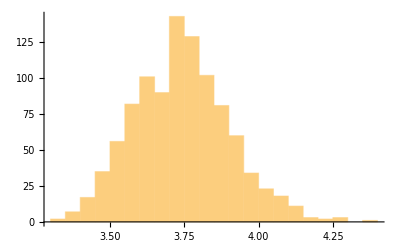

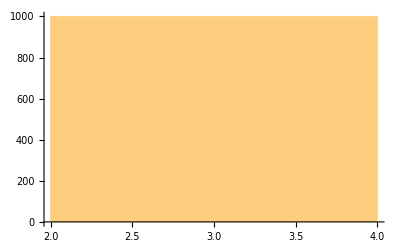

```mathematica
G1=RandomGraph[SpatialGraphDistribution[200,0.115],1000,EdgeWeight->{_:> RandomInteger[{1,5}]}];
G2=RandomGraph[WattsStrogatzGraphDistribution[200,0.135],1000,EdgeWeight->{_:> RandomInteger[{1,5}]}];
Histogram[EdgeCount/@G1/VertexCount/@G1//N,Automatic]
Histogram[EdgeCount/@G2/VertexCount/@G2//N,Automatic]
```

```mathematica
Tablize[data_]:=TextGrid[{{"Label", "Total Time","CPU Time"}}~Join~data];
```

```mathematica
(* Built-in Methods *)
```

```mathematica
TableItem[label_,method_,set_]:={label,(AbsoluteTiming[FindSpanningTree[#,Method-> method]&/@set;])[[1]],(Timing[FindSpanningTree[#,Method-> method]&/@set;])[[1]]}
```

```mathematica
Tablize[TableItem@@@{
{"G1 Built-in Kruskal","Kruskal",G1},
{"G2 Built-in Kruskal","Kruskal",G2},
{"G1 Built-in Prim","Prim",G1},
{"G2 Built-in Prim","Prim",G2}
}
]
```

Label | Total Time | CPU Time
G1 Built-in Kruskal | 0.522785 | 0.15625
G2 Built-in Kruskal | 0.397258 | 0.03125
G1 Built-in Prim | 0.536917 | 0.234375
G2 Built-in Prim | 0.473338 | 0.0625

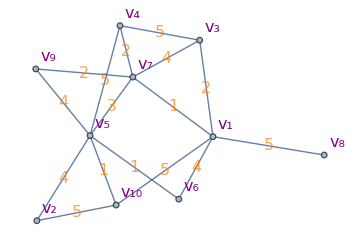

```mathematica
S1=Block[{n=10,m=16,label = Directive[FontSize->16,FontFamily->"Consolas"]},RandomGraph[UniformGraphDistribution[n,m],ImageSize->Medium,EdgeWeight->{_:> RandomInteger[{1,5}]},
EdgeLabels->"EdgeWeight",VertexLabels->Table[i->Subscript[v, i],{i,1,10}],
 EdgeLabelStyle->Directive[label,Orange],VertexLabelStyle->Directive[label,Purple]
]
]
```

```mathematica
{VertexList[S1],EdgeList[S1]}
```

{{1,2,3,4,5,6,7,8,9,10},{1<->3,1<->6,1<->7,1<->8,1<->10,2<->5,2<->10,3<->4,3<->7,4<->5,4<->7,5<->6,5<->7,5<->9,5<->10,7<->9}}

```mathematica
SetOptions[HighlightGraph,EdgeShapeFunction->({RGBColor[1,0.52,0.51],Line[#1]}&),VertexShapeFunction->({RGBColor[1,0.52,0.51],PointSize[Large],Point[#1]}&),ImageSize->Medium];
```

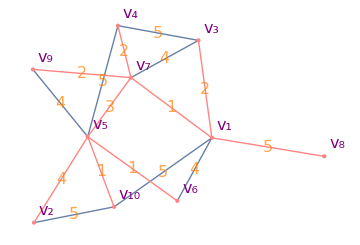
{-Graphics-,-Graphics-}

```mathematica
{HighlightGraph[S1,FindSpanningTree[S1,Method-> "Kruskal"]],
HighlightGraph[S1,FindSpanningTree[S1,Method-> "Prim"]]}
```

```mathematica
Boruvka[graph_]:=Module[{G=graph,vs=VertexList[graph],es=EdgeList[graph]},
mst=Partition@@{es,1};

]
```

```mathematica
DFS[graph_]:=Module[{G=graph,vs=VertexList[graph],es=EdgeList[graph]},
index=0;
flags = Table[1,Length[vs]];
components={};

aes=(Transpose@{#1,#2}~Join~Transpose@{#2,#1})&[EdgeList[S1][[All,1]],EdgeList[S1][[All,2]]];

]
```